a)

{{x→InterpolatingFunction[…]}}

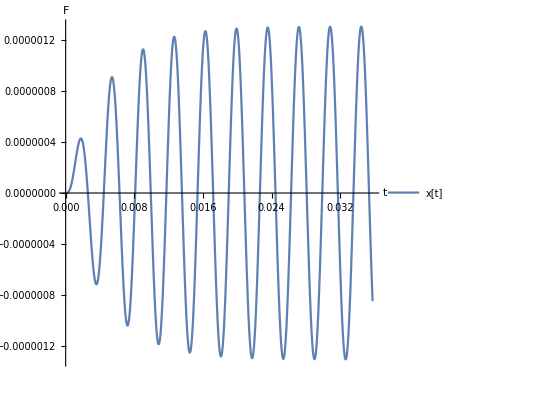

b)

{{x→InterpolatingFunction[…]}}

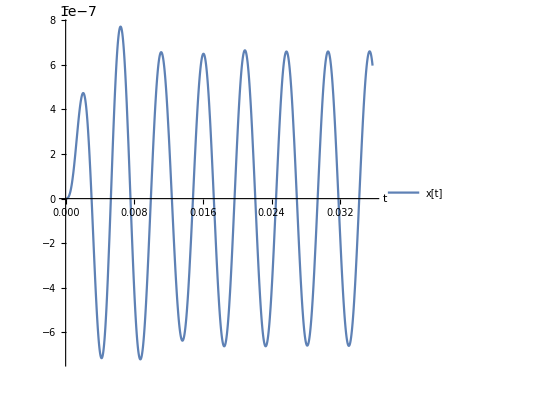

c)

{{x→InterpolatingFunction[…]}}

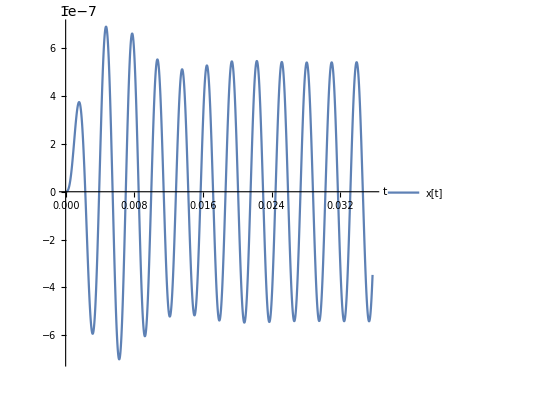

ω    |     X_0

172.841 | 3.29214×10^-7
345.682 | 3.33245×10^-7
518.523 | 4.05995×10^-7
691.364 | 4.55362×10^-7
864.206 | 4.79099×10^-7
1037.05 | 4.85455×10^-7
1209.89 | 6.76731×10^-7
1382.73 | 7.67327×10^-7
1555.57 | 1.08512×10^-6
1728.41 | 1.30649×10^-6
1901.25 | 1.04765×10^-6
2074.09 | 7.852×10^-7
2246.93 | 6.323×10^-7
2419.78 | 5.05963×10^-7
2592.62 | 4.48396×10^-7
2765.46 | 3.93726×10^-7
2938.3 | 3.42918×10^-7
3111.14 | 2.96148×10^-7
3283.98 | 2.57102×10^-7

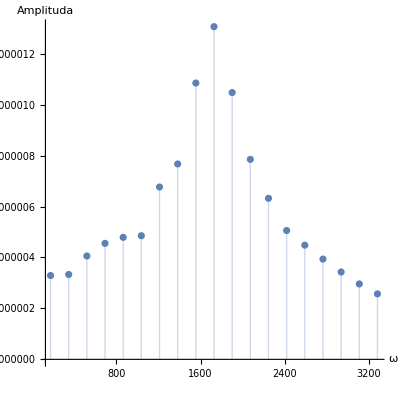

X_0

1.30649×10^-6

ω dla X_0

{1728.41}

ω_-

2216.01

ω_+

1270.1

Δω

945.908

```mathematica
Subscript[N, 0]=5;
Subscript[nralbumu, 1]=136831;
Subscript[nralbumu, 2]=136693;
Subscript[nralbumu, 3]=132339;
Subscript[nralbumu, 4]=136681;
Subscript[nralbumu, 5]=136693;
s=(∑_(i=1)^Subscript[N, 0] Subscript[nralbumu, i])/Subscript[N, 0];
Δs=√((∑_(i=1)^Subscript[N, 0] (Subscript[nralbumu, i]-s)^2)/Subscript[N, 0]);
Subscript[ω, 0]=Δs+1;
b=Subscript[ω, 0]/4;
f=1;
n=10;
timelimit=(n*(2 π))/Subscript[ω, 0];
(*a*)
Subscript[ω, 0]=Δs+1;
ω=√(Subscript[ω, 0]^2-b^2/2);
Print["a)"]
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t ω],x[0]==0,x'[0]==0},x,{t,0,timelimit}]
Plot[Evaluate[{x[t]}/.s],{t,0,timelimit},PlotStyle->Automatic,PlotRange->All,AspectRatio->1,AxesLabel->{"t","F"},PlotLegends->{"x[t]"}]
(*b*)
Subscript[ω, 0]=Δs+1;
Print["b)"]
ω=3/4 √(Subscript[ω, 0]^2-b^2/2);
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t ω],x[0]==0,x'[0]==0},x,{t,0,timelimit}]
Plot[Evaluate[{x[t]}/.s],{t,0,timelimit},PlotStyle->Automatic,PlotRange->All,AspectRatio->1,AxesLabel->{"t","F"},PlotLegends->{"x[t]"}]

(*c*)
Subscript[ω, 0]=Δs+1;
Print["c)"]
ω=5/4 √(Subscript[ω, 0]^2-b^2/2);
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t ω],x[0]==0,x'[0]==0},x,{t,0,timelimit}]
Plot[Evaluate[{x[t]}/.s],{t,0,timelimit},PlotStyle->Automatic,PlotRange->All,AspectRatio->1,AxesLabel->{"t","F"},PlotLegends->{"x[t]"}]
(*2*)
alist={};
ωlist={};
Subscript[ω, 0]=Δs+1;
timelimit=(n*(2 π))/Subscript[ω, 0];
For[k=1,k≤19,k++,
Subscript[ω, 0]=Δs+1;
b=Subscript[ω, 0]/4;
ω=(k/10)*Sqrt[Subscript[ω, 0]^2-(1/2)*b^2];
ωlist=Append[ωlist,N[ω]];
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t ω],x[0]==0,x'[0]==0},x,{t,0,timelimit}];
amplituda=First[NMaximize[{Abs[x[t]]/.s[[1]],0<t<timelimit},t]];
alist=Append[alist,amplituda];]
dane=Transpose[{ωlist,alist}];
Print["    ω    |     X_0"]
Grid[dane,Frame->All]
ListPlot[dane,PlotStyle->Automatic,PlotRange->All,AspectRatio->1,AxesLabel->{"ω","Amplituda"},Filling->Axis]




(*3*)
Print["X_0"]
max=Max[alist]
index=Position[alist,max];
index=index[[1]];
index=index[[1]];
timelimit=(n*(2 π))/Subscript[ω, 0];
Print["ω dla X_0"]
Subscript[ω, max]=ωlist[[{index}]]
polowamax=1/2*max;
Subscript[ω, temp]=Subscript[ω, max][[1]];
test=max;
While[test>polowamax,
Subscript[ω, temp]=Subscript[ω, temp]*1.001;
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t *Subscript[ω, temp]],x[0]==0,x'[0]==0},x,{t,0,timelimit}];
test=First[NMaximize[{Abs[x[t]]/.s[[1]],0<t<timelimit},t]];
]
While[test<polowamax,
Subscript[ω, temp]=Subscript[ω, temp]*0.999999;
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t *Subscript[ω, temp]],x[0]==0,x'[0]==0},x,{t,0,timelimit}];
test=First[NMaximize[{Abs[x[t]]/.s[[1]],0<t<timelimit},t]];
]
Print["ω_-"]
SubMinus[ω]=Subscript[ω, temp]
polowamax=1/2*max;
Subscript[ω, temp]=Subscript[ω, max][[1]];
test=max;
While[test>polowamax,
Subscript[ω, temp]=Subscript[ω, temp]*0.999;
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t *Subscript[ω, temp]],x[0]==0,x'[0]==0},x,{t,0,timelimit}];
test=First[NMaximize[{Abs[x[t]]/.s[[1]],0<t<timelimit},t]];]
While[test<polowamax,
Subscript[ω, temp]=Subscript[ω, temp]*1.000001;
s=NDSolve[{b x'[t]+x''[t]+Subscript[ω, 0]^2 x[t]==f Sin[t *Subscript[ω, temp]],x[0]==0,x'[0]==0},x,{t,0,timelimit}];
test=First[NMaximize[{Abs[x[t]]/.s[[1]],0<t<timelimit},t]];

]
Print["ω_+"]
SubPlus[ω]=Subscript[ω, temp]
Print["Δω"]
Δω=Abs[SubPlus[ω]-SubMinus[ω]]
```